Exercises for Section 4 | Displaying Lists

Make a bar chart of {1,1,2,3,5}. |

EXPECTED OUTPUT »

-Graphics- | ×

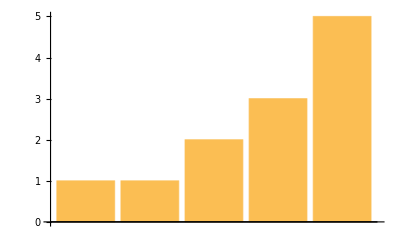

```mathematica
BarChart[{1,1,2,3,5}]
```

Make a pie chart of numbers from 1 to 10. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
PieChart[Range[10]]
```

-Graphics-

Make a bar chart of numbers counting down from 20 to 1. |

EXPECTED OUTPUT »

-Graphics- | ×

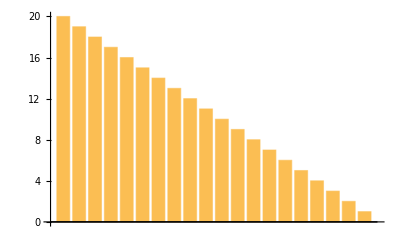

```mathematica
BarChart[Reverse[Range[20]]]
```

Display numbers from 1 to 5 in a column. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Column[Range[5]]
```

1
2
3
4
5

Make a number line plot of the squares {1,4,9,16,25}. |

EXPECTED OUTPUT »

-Graphics- | ×

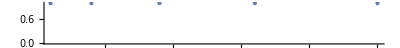

```mathematica
NumberLinePlot[{1,4,9,16,25}]
```

Make a pie chart with 10 identical segments, each of size 1. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
PieChart[List[1,1,1,1,1,1,1,1,1,1]]
```

-Graphics-

Make a column of pie charts with 1, 2 and 3 identical segments. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Column[List[PieChart[List[1]],PieChart[List[1,1]],PieChart[List[1,1,1]]]]
```

-Graphics-

Make a list of pie charts with 1, 2 and 3 identical segments. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
List[PieChart[List[1]],PieChart[List[1,1,]],PieChart[List[1,1,1]]]
```

{-Graphics-,-Graphics-,-Graphics-}

Make a bar chart of the sequence 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1. |

EXPECTED OUTPUT »

-Graphics- | ×

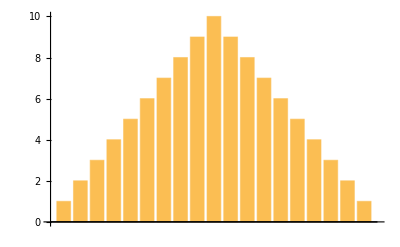

```mathematica
BarChart[Join[Range[10],Reverse[Range[9]]]]
```

Make a list of a pie chart, bar chart and line plot of the numbers from 1 to 10. |

EXPECTED OUTPUT »

-Graphics- | ×

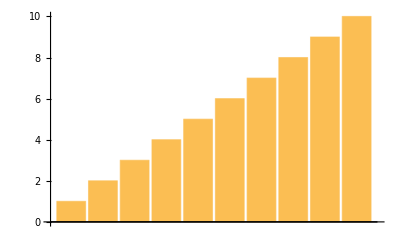
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
List[PieChart[Range[10]],BarChart[Range[10]],ListLinePlot[Range[10]]]
```

Make a list of a pie chart and a bar chart of {1,1,2,3,5,8,13,21,34,55}. |

EXPECTED OUTPUT »

-Graphics- | ×

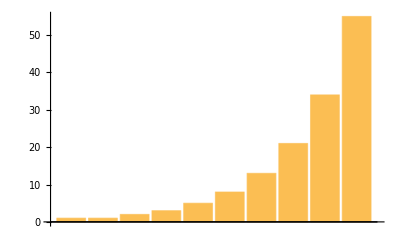
{-Graphics-,-Graphics-}

```mathematica
List[PieChart[List[1,1,2,3,5,8,13,21,34,55]],BarChart[List[1,1,2,3,5,8,13,21,34,55]]]
```

Make a column of two number line plots of {1,2,3,4,5}. |

EXPECTED OUTPUT »

-Graphics- | ×

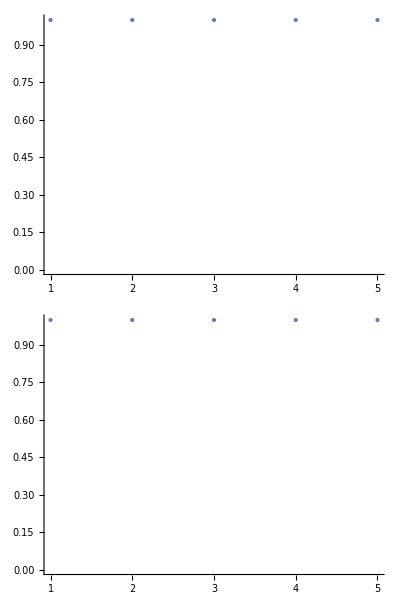

```mathematica
Column[List[NumberLinePlot[Range[5]],NumberLinePlot[Range[5]]]]
```

Make a number line of fractions 1/2, 1/3, ... through 1/9. |

EXPECTED OUTPUT »

-Graphics- | ×

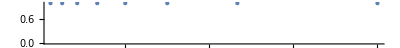

```mathematica
NumberLinePlot[List[1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9]]
```